# Solving TOV equations.

#### Constants

```mathematica
(* Universal constants*)
G = 6.6743 10^-8;
c = 2.99792458 10^10;

(* Astronomical parameters*)
Subscript[M, Earth]=5.9724*^27;
Subscript[R, Earth] = 6.371*^8;
Subscript[M, Jupiter]=1.8982*^30;
Subscript[R, Jupiter]=6.991*^9;
Subscript[M, sun]= 1.9885*^33;
Subscript[R, sun]=6.957*^10;

α=G Subscript[M, sun]/(10^5 c^2);
Subscript[E0, sol]= Subscript[M, sun] c^2;

(* Nuclear parameters*)
mp=1.67262192369 10^-24;
mn=1.67492749804 10^-24;
me = 9.1093837015  10^-28;
λp=2.10308910336 10^-14;
λn =2.1001941552  10^-14;
λe = 3.8615926796  10^-11;

km = 10.0^5;
km3 = (10.0^5)^3;
rmin = 0.001;
rmax = 350;
densup = 7.860;
```

## 1 Equations of state:

## 1.1 Equation of state 1: Free gas of neutrons

#### 1.1.1 Relativistic Case (pure NS)

Let’s try first just this one: relativistic case

```mathematica
Pressure R[ϵ_]:=ϵ/3;
Density R[p_]:=3p;
```

#### 1.1.2 Non Relativistic Case (pure NS)

Pressure and density take the following form

```mathematica
ϵ(P) = 5 (m/(15 π^2 λ^3))^(2/5)P^(3/5)
```

with m, λ of the gas we are considering, let’s say neutrons only, then

```mathematica
kf[m_,l_]:=5((m c^2)/(15 π^2 l^3))^(0.4);
kn=kf[mn,λn];
kp=kf[mp,λp];
ke=kf[me,λe];

Density NR[p_]:=kn p^0.6
```

#### 1.1.3 Whole Range Neutron Star (Pure NS)

We need first to define density and pressure as function of non-dimensional fermi momentum

```mathematica
nfun[m_,l_]:= (m c^2)/(8 π^2 l^3)
epsilon i[z_,m_,l_]:= nfun[m,l]((2 z^3 + z )Sqrt[1 +z^2] - ArcSinh[z])
pressure i[z_,m_,l_]:=nfun[m,l]((2z^3 /3-z)Sqrt[1+z^2]+ArcSinh[z])
```

now, we create a table of data (p, ϵ):

```mathematica
ListEoS n={};
Do[ ListEoS n=Union[ListEoS n,Table[{pressure i[z,mn,λn],epsilon i[z,mn,λn]},{z,10.^i,10^(i+1)-10^(i-1),10^(i-2)}]],{i,-3,2}]
EoS n=Interpolation[ListEoS n,InterpolationOrder->1];
```

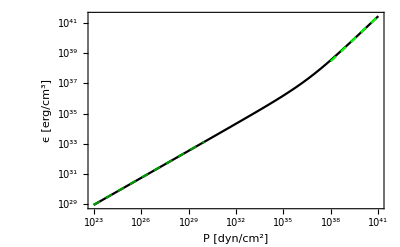

```mathematica
DNR=LogLogPlot[Density NR[x],{x,10^23, 10^30},
PlotStyle->{RGBColor[0.,0.6,0.],Dashed},
PlotLegends->Placed[{"Non Relativistic"},{Left,Top}]];
DR =LogLogPlot[Density R[x],{x,10^38, 10^41},
PlotStyle->{RGBColor[0.,1,0.], Dashed},
PlotLegends->Placed[{"Relativistic"},{Left,Top}]];
DNS=LogLogPlot[{EoS n[x]},{x,10^23,10^41},
PlotLegends->Placed[{"Whole range"},{Left,Top}],
PlotStyle->{ Black}];
EOSn =Show[{DNS,DNR, DR},
FrameLabel->{"P [dyn/cm^2]","ϵ [erg/cm^3]"},
Frame->True,
PlotTheme->"Scientific"]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/3-Neutron Stars Densities/Plots/equation_of_state_n_m.pdf", EOSn];
```

Now, let’s build the function for the whole range as a piecewise function taking the R and NR approx,

```mathematica
pw=Piecewise[{{Density NR[x], 0≤  x<10^23}, {EoS n[x],10^23≤ x≤ 10^45},{Density R[x],x>10^45}}];
dener n[p_]:=pw/.x-> p
```

Now we can proceed to do the numerical integration

## 1.2 Equation of state 2: Free gas of npe

```mathematica
Zp[z_,mn_,mp_,me_]:=Sqrt[(mn^2 (1+z^2) - (me^2 + mp^2))^2-4 mp^2 me^2 ]/(2 mp mn Sqrt[1 + z^2])
Ze[z_,mn_,mp_,me_]:=mp/me Zp[z,mn,mp,me]

epsilon pe[z_]:=  epsilon i[z,mp,λp]+epsilon i[mp/me z, me, λe]
pressure pe[z_]:=pressure i[z,mp,λp]+pressure i[mp/me z ,me,λe]

epsilon npe[z_]:= epsilon i[z,mn,λn]+ epsilon i[Zp[z,mn,mp,me],mp,λp]+epsilon i[mp/me Zp[z,mn,mp,me],me,λe]
pressure npe[z_]:=pressure i[z,mn,λn]+pressure i[Zp[z,mn,mp,me],mp,λp]+pressure i[mp/me Zp[z,mn,mp,me],me,λe]
```

Non relativistic regime (before z_critical=Zc)

```mathematica
Zc=Zp[0,mn,mp,me]
{pressure pe[Zc],pressure npe[0]}
```

0.0012654

{3.03851×10^24,3.03851×10^24}

```mathematica
ListEoS npe=Table[{pressure pe[z],epsilon pe[z]},{z,0,Zc,10^-6}];
Do[ ListEoS npe=Union[ListEoS npe,Table[{pressure npe[z],epsilon npe[z]},{z,10.^i,10^(i+1)-10^(i-1),10^(i-2)}]],{i,-3,2}]
dener npe=Interpolation[ListEoS npe,InterpolationOrder->1];
```

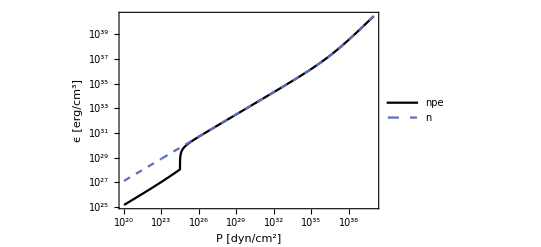

```mathematica
EOSnpe = LogLogPlot[{dener npe[x],dener n[x]},{x,10^20,10^40},
Frame->True,
FrameLabel->{"P [dyn/cm^2]","ϵ [erg/cm^3]"},
PlotStyle->{Black,Dashed},
PlotLegends->Placed[{"npe", "n"},{Left,Top}],
PlotTheme->"Scientific"]
```

```mathematica
Export["Plots/equation_of_state_npe_m.pdf",EOSnpe];
```

## 1.3 Equation of state 3: Interacting protons and neutrons

Auxiliary constants and functions

```mathematica
λN =2.1001941552  10^-1;  (*in fm*)
hbarc = 197.3269804 ;(*MeV fm*)

A := -46.65
B:=39.54
Bp:=0.3
σ := 1.663
C1:=-83.84
C2:=23.65
n0:=0.16
Subscript[pF, 0]:=263
mN :=939
EF:=3/5 Subscript[pF, 0]^2/(2 mN)
Λ1 :=1.5 Subscript[pF, 0]
Λ2 :=3 Subscript[pF, 0]
pF[n_]:= Subscript[pF, 0] (n/n0)^(1/3)
n[z_]:= z^3/(3 π^2 λN^3)
z[n_,l_]:= (3 π^2 l^3 n)^1/3
```

Energy density per baryon as function of baryon density:

```mathematica
EHalf[n_]:= mN+ EF (n/n0)^(2/3)+A/2 n/n0+ (B (n/n0)^σ)/(1 + Bp (n/n0)^(σ-1))+ 3 C1 (Λ1/Subscript[pF, 0])^3(pF[n]/Λ1-ArcTan[pF[n]/Λ1])+ 3 C2 (Λ2/Subscript[pF, 0])^3(pF[n]/Λ2-ArcTan[pF[n]/Λ2])
ESym[n_]:= 13 (n/n0)^(2/3)+ 17 n/n0
β[n_]:=(3 π^2 hbarc^3)/64 (13/n0^(2/3) n^(1/3) + 17/n0 n^(2/3))^-3
γ[n_]:=Sqrt[1+(2β[n])/27]
Yp[n_]:=1/2-1/4((4/27 β[n]^2/(γ[n]-1))^(1/3)-(2β[n](γ[n]-1))^(1/3))
ϵb[n_]:= n(EHalf[n]+(1-2Yp[n])^2 ESym[n] )
```

Pressure as function of baryon density, and in terms of energy density

```mathematica
Pb[n_]:= n((2EF)/3(n/n0)^(2/3)+A/2(n/n0)+ (σ B (n/n0)^σ)/(1 + Bp (n/n0)^(σ-1))-((σ-1) B Bp(n/n0)^(2σ-1))/((1 + Bp (n/n0)^(σ-1))^2)+  ( C1/(1 + (Subscript[pF, 0]/Λ1)^2(n/n0)^(2/3))+ C2/(1 + (Subscript[pF, 0]/Λ2)^2(n/n0)^(2/3)))(n/n0))+(1-2 Yp[n])^2 (26/3 n^(5/3)/n0^(2/3)+17 n^2/n0)
```

Conversion factors

```mathematica
MeVToErg:=1.6022 10^-6
fmTocm := 10^-13
MeVfmTocgs:= MeVToErg/fmTocm^3
```

Total energy density and pressure

```mathematica
ϵT[z_]:= ϵb[n[z]]*MeVfmTocgs +epsilon i[mp/me Zp[z,mn,mp,me],me,λe]
PT[z_]:= Pb[n[z]]*MeVfmTocgs+pressure i[mp/me Zp[z,mn,mp,me],me,λe]
```

List of z values and interpolation

```mathematica
{ϵb[n[10^-6]],epsilon i[mp/me Zp[10^-6,mn,mp,me],me,λe], epsilon i[10^-6,mn,λn]}
```

{3.42347×10^-15,1.22004×10^25,5.48875×10^18}

```mathematica
ListEoS int={};
ListEoS int=Table[{PT[z],ϵT[z]},{z,10^-6,10^-5,10^-6}];
Do[ ListEoS int=Union[ListEoS int,Table[{PT[z],ϵT[z]},{z,10.^i,10^(i+1)-10^(i-1),10^(i-2)}]],{i,-2,1}]
EoSint=Interpolation[ListEoS int,InterpolationOrder->1];
```

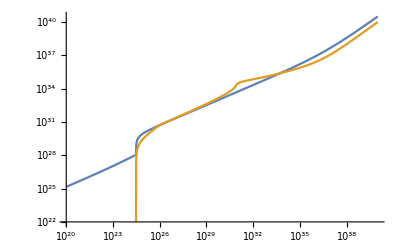

```mathematica
LogLogPlot[{dener npe[x],EoSint[x]},{x,10^20,10^40}]
```

```mathematica
pw2=Piecewise[{{Density NR[x], 0≤  x<10^26}, {EoSint[x],6 10^25≤ x≤ 10^45}}];
dener int[p_]:=pw2/.x-> p
```

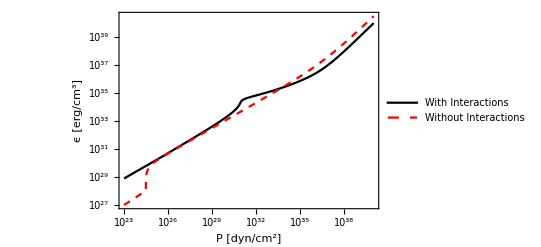

```mathematica
EOS int = LogLogPlot[{dener int[x],dener npe[x]},{x,10^23,10^40},
Frame->True,
FrameLabel->{"P [dyn/cm^2]","ϵ [erg/cm^3]"},
PlotStyle->{Black,{Dashed,Red}},
PlotLegends->Placed[{"With Interactions", "Without Interactions"},{Left,Top}],
PlotTheme->"Scientific"]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/3-Neutron Stars Densities/Plots/equation_of_state_int_m.pdf",EOS int]
```

/home/nicolas/Documents/Physics/Bachelors-Dissertation/3-Neutron Stars Densities/Plots/equation_of_state_int_m.pdf

## 2. Hydrostatic Equilibrium equation

## 2.1 Newton Equations:

We solve first this simple case.

```mathematica
Pc = 3.3 10^34;
ListRG={};
Do[
Do[{
solutionN = NDSolve[{p'[r]== If[p[r]>0,-(α dener[p[r]*Pc]*M[r])/(Pc r^2),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],p[rmin]==1,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
mass ad[x_]:=M[x]/.solutionN[[1]];
pressure ad[x_]:=p[x]/.solutionN[[1]];
If[pressure ad[rad]==0,
Print["Central Pressure = ", Pc, "\n",
	"Radius in km = ", rad, "\n",
	"Mass in M_s = ", mass ad[rad]];
Break[],
ListRG=Append[ListRG,{rad,dener[Pc*pressure ad[rad]]}]
];
},
{rad,1,25,.1}],{dener,{dener n,dener npe,dener int}}]
```

Central Pressure = 3.3×10^34
Radius in km = 14.8
Mass in M_s = 0.804716

Central Pressure = 3.3×10^34
Radius in km = 14.7
Mass in M_s = 0.797783

Central Pressure = 3.3×10^34
Radius in km = 13.7
Mass in M_s = 1.34561

## 2.2 TOV equations and density

### 2.2.1 Equation of state with only neutrons

Computation with precision of masses and radii

```mathematica
ListPc ={ 10.^35,10.^36, 10.^38, 10.^40};
Do[{
Do[{
Do[{
Pc = ListPc[[ñ]];
(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(**** Interpolation of solutions****)
mass[x_]=M[x]/.solutionTOV[[1]];
TOVpressure[x_]:=p[x]/.solutionTOV[[1]];

(**** Integrate until surface ****)
If[TOVpressure[rad]==0,
Break[],
R = rad;
MT = mass[rad]
];
},{rad,rmin+.1,30,.1}];
Print[Pc, "\t",R, "\t",MT]
},{dener,{dener n,dener npe,dener int}}]}
,{ñ,1,Length[ListPc]}]
```

1.×10^35	11.301	0.67462

1.×10^35	11.301	0.66734

1.×10^35	12.101	1.41699

1.×10^36	7.601	0.688034

1.×10^36	7.601	0.674752

1.×10^36	10.301	1.99622

1.×10^38	5.101	0.378702

1.×10^38	5.101	0.368548

1.×10^38	7.601	1.37783

1.×10^40	6.201	0.440421

1.×10^40	6.301	0.430667

1.×10^40	8.001	1.45659

Computation of density and mass distribution for different Pc, gives the same for both EOS

```mathematica
ListPc ={ 10.^35,10.^36, 10.^38, 10.^40};
Listϵ=Table[0,{n,Length[ListPc]}];
Listm=Table[0,{n,Length[ListPc]}];

Do[{
Localϵ={};
Localm={};
Do[{
Pc = ListPc[[ñ]];
dener=dener int;
(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(**** Interpolation of solutions****)
mass[x_]=M[x]/.solutionTOV[[1]];
TOVpressure[x_]:=p[x]/.solutionTOV[[1]];

(**** Integrate until surface ****)
If[TOVpressure[rad]==0,
Break[],
Localϵ=Append[Localϵ,{rad,dener[Pc*TOVpressure[rad]]/Pc}];
Localm=Append[Localm,{rad,mass[rad]}];
];
},{rad,rmin+.01,30,.1}],
Listϵ[[ñ]]=Localϵ;
Listm[[ñ]]=Localm
},{ñ,1,Length[ListPc]}]
```

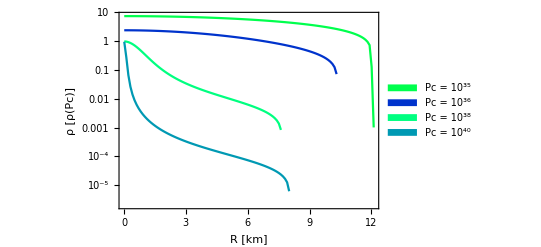

```mathematica
DensityNS int =ListLogPlot[{ Listϵ[[1]],Listϵ[[2]],Listϵ[[3]],Listϵ[[4]]},
PlotStyle->{RGBColor[0,1,0.3],RGBColor[0,0.2,0.8],RGBColor[0,1,0.5],RGBColor[0,0.6,0.7]},
Joined->True,
Frame->True,
FrameLabel->{"R [km]", "ρ [ρ(Pc)]"},
PlotLegends->Placed[SwatchLegend[{RGBColor[0,1,0.3],RGBColor[0,0.2,0.8],RGBColor[0,1,0.5],RGBColor[0,0.6,0.7]},
{"Pc = 10^35 ","Pc = 10^36 ","Pc = 10^38", "Pc = 10^40"},
LegendMarkers->"Bubble",
LegendMarkerSize->10,
LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],
{Right, Bottom}]]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/3-Neutron Stars Densities/Plots/densityNS_int.pdf",DensityNS int];
```

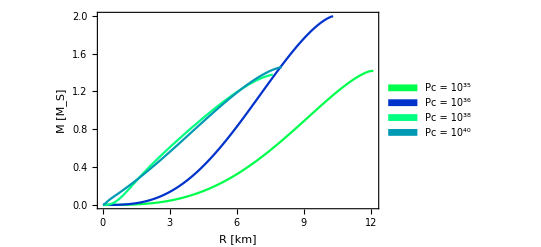

```mathematica
MassNS=ListPlot[{Listm[[1]],Listm[[2]], Listm[[3]],Listm[[4]]},PlotStyle->{RGBColor[0,1,0.3],RGBColor[0,0.2,0.8],RGBColor[0,1,0.5],RGBColor[0,0.6,0.7]},
Joined->True,
Frame->True,
FrameLabel->{"R [km]", "M [M_S]"},
PlotLegends->Placed[SwatchLegend[{RGBColor[0,1,0.3],RGBColor[0,0.2,0.8],RGBColor[0,1,0.5],RGBColor[0,0.6,0.7]},
{"Pc = 10^35 ","Pc = 10^36 ","Pc = 10^38", "Pc = 10^40"},
LegendMarkers->"Bubble",
LegendMarkerSize->10,
LegendFunction->(Framed[#,RoundingRadius->5]&),LegendMargins->5],
{Right, Bottom}]]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/3-Neutron Stars Densities/Plots/MassNS_int.pdf",MassNS];
```

## 2.3 Traversal Times

### 2.3.1 Theory

The equations to solve are, in non dimensional form

```mathematica
(d p)/(d r)= -(α [M(r) + β(Pc) r^3 p(r)][ϵ(p(r)) + p(r)][r^2 - 2 α r M(r)])^-1
```

This gives us non dimensional pressure and energy density. Along with the non-dimensional mass, this will be useful to define the metric tensor component functions:

```mathematica
Subscript[g, rr](r)=A(r) = (1 - (2 G M(r))/r)^-1 = (1 - 2α (M̄)/r)^-1
```

with M̄ in units of solar masses and r in km. And the other function comes from the diff. eq.

```mathematica
(B'(r))/(B(r))= - (2 P'(r))/(P(r)+ϵ(r))
```

with boundary conditions in the surface equal to the Schwarzschild solution for the exterior metric.
Given  A=g_rr and B=g_tt, we already have all the components of the metric. The general energy diff. eq. is

```mathematica
1/2(dr/dτ)^2+1/2 g^rr(r)(1 - g^tt(r) E^2)c^2=0
```

from this energy-like equation, consider the potential part, at the turning points (r=R),

```mathematica
V(R) = 1/2 g^rr(R)(1 - g^tt(R) E^2)c^2=0
E^2= 1/(g^tt(R))= Subscript[g, tt](R) 
-> E^2 = B(R)
```

we have therefore the following integral:

```mathematica
Δτ = 2/c∫(√(-Subscript[g, tt](r)))/(√(1 - E^2/Subscript[g, rr](r)))ⅆr
Δτ = 2/c(∫_0)^R(√(A(r)B(r)))/(√(B(R)- B(r)))ⅆr
```

that gives us proper times in seconds.

### 2.2.2 Numerical Computation

Schwarzschild times

```mathematica
Rhat[R_, M_]:= Sqrt[(G M)/(c^2 R)]
Em[R_]:=√(1-2 R^2)
x[r_,R_]:= Sqrt[1-2r^2]/Sqrt[1-2 R^2]
ω [R_,M_] :=Sqrt[ (G M)/R^3]
τ[R_]:=2 Re[NIntegrate[1/(x[r,R] Em[R])(3-x[r,R])/Sqrt[(5-x[r,R])(x[r,R]-1)],{r,0,R},WorkingPrecision->10, AccuracyGoal->20]]

t[R_]:= 2 NIntegrate[Re[4/(Em[R]^2x[r,R](3-x[r,R])Sqrt[(5 - x[r,R])(x[r,R]-1)] )],{r,0,R},WorkingPrecision->10, AccuracyGoal->20]
```

```mathematica
{t[0.41],t[0.53]}
```

{3.841190637,4.83719308}

The following is the code that returns proper times for some NS’s with different central pressures:

```mathematica
ListPc ={ 10.^35, 10.^36, 10.^38, 10.^40,10.^42};
Do[{
Pc = ListPc[[ñ]];

Print["NS ", ñ, " - Central Pressure: ", ScientificForm[Pc]]; 

Do[{

Do[{
(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(**** Interpolation of solutions****)
mass[x_]=M[x]/.solutionTOV[[1]];
pressure[x_]:=p[x]/.solutionTOV[[1]];

(**** Integrate until surface ****)
If[pressure[rad]≤0,
Break[],
(*Print[rad, "\t", pressure[rad],"\t",density[rad]];
Listϵ=Append[Listϵ,{rad,dener[Pc*pressure[rad]]/Pc}];
Listp=Append[Listp,{rad,pressure[rad]}];*)
{capR=rad}];
},{rad,7.,rmax,.01}];
radius = capR/1.5;rstep=0.001;
While[dener[pressure[radius] Pc]/c^2≥ densup ,
(*Print["radius = " , radius, "\t density = ",dener[pressure[radius] Pc]/c^2] ;*) 
radius=radius+rstep];

pres[x_]:=pressure[x];
ϵps[x_]:=dener int[Pc*pressure[x]]/Pc;

R= radius-rstep;
MStar=mass[R];

Print["R(km) = ", R, "\n",
	"M(M_s) =", MStar, "\n",
	"R̂     =  ", Rhat[R km, MStar*Subscript[M, sun]]];


(**** Metric coefficients ****)

grr[r_]:= (1 - 2 α mass[r]/r)^-1;

Bmax =1- (2 α)/R;
BFunction=NDSolve[ {Bb'[r] == -2 Bb[r] pres'[r]/(pres[r]+ϵps[r]),Bb[R]==Bmax},Bb[r],{r,rmin,R}];
gtt[r_]=Bb[r]/.BFunction[[1]];
(****Computing times ****)

τsNS =2 NIntegrate[Sqrt[grr[r] gtt[r]/(gtt[R]-gtt[r])],{r,rmin,R},MaxRecursion->20]/(10^(-5) c);
tsNS =2 NIntegrate[Sqrt[grr[r] gtt[R]/(gtt[r](gtt[R]-gtt[r]))],{r,rmin,R},MaxRecursion->20]/(10^(-5) c);

Print["τ (ms): ", τsNS 10^3,"\n",
	"t  (ms): ", tsNS 10^3, "\n",
	"τs (ms): ", τ[Rhat[R km, MStar*Subscript[M, sun]]] 10^3/ω[R km, MStar*Subscript[M, sun]],"\n",
	"ts (ms): ", t[Rhat[R km, MStar*Subscript[M, sun]]]10^3/ω[R km, MStar*Subscript[M, sun]],"\n",
"----------------------------------------"]},{dener,{dener npe,dener int}}]
},{ñ,1,Length[ListPc]}]
```

NS 1 - Central Pressure: 1.×10^35

R(km) = 11.3247
M(M_s) =0.66734
R̂     =  0.294989

τ (ms): 0.385376
t  (ms): 0.485158
τs (ms): 0.380694
ts (ms): 0.440801
----------------------------------------

Computation of times vs central pressure and radius vs central pressure

```mathematica
ListPc =Flatten[{Table[n * 10.^38,{n,1,9,2}],Table[n * 10.^39,{n,1,9,2}],Table[n * 10.^40,{n,1,9,2}],Table[n * 10.^41,{n,1,9,2}],Table[n * 10.^42,{n,1,9,2}],Table[n * 10.^43,{n,1,9,2}], Table[n * 10.^44,{n,1,9,2}]}];
Analystnpe = {};
Do[{
Pc = ListPc[[ñ]];

Do[{
dener=dener npe;
(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(**** Interpolation of solutions****)
mass[x_]=M[x]/.solutionTOV[[1]];
pressure[x_]:=p[x]/.solutionTOV[[1]];

(**** Integrate until surface ****)
If[pressure[rad]==0,
Break[],
capR=rad;
];
},{rad,1,30,.01}];
radius = capR/1.5;rstep=0.001;
While[dener[pressure[radius] Pc]/c^2≥ densup ,
(*Print["radius = " , radius, "\t density = ",dener[pressure[radius] Pc]/c^2] ;*)
radius=radius+rstep];

R=radius-rstep;
MStar=mass[R];
ϵ n[x_]:=dener int[pressure[x] Pc]/Pc;

(**** Metric coefficients ****)

grr[r_]:= (1 - 2 α mass[r]/r)^-1;

Bmax =1- (2 α)/R;
BFunction=NDSolve[ {Bb'[r] == -2 Bb[r] pressure'[r]/(pressure[r]+ϵ n[r]),Bb[R]== Bmax},Bb[r],{r,rmin,R}];
gtt[r_]=Bb[r]/.BFunction[[1]];

(****Computing times ****)

ts=t[Rhat[R km, MStar*Subscript[M, sun]]];
tsNS =2 NIntegrate[Sqrt[grr[r] gtt[R]/(gtt[r](gtt[R]-gtt[r]))],{r,rmin,R},MaxRecursion->20]/(10^(-5) c);

Print[Pc,"\t", ts/ω[R km, MStar*Subscript[M, sun]],"\t", tsNS],
Analystnpe = Append[Analystnpe,{Pc,tsNS 10^3 }]
},{ñ,1,Length[ListPc]}]
```

1.×10^38	0.000185815	0.000350518

3.×10^38	0.00022766	0.000403604

5.×10^38	0.000244721	0.000422728

7.×10^38	0.000251775	0.000433721

9.×10^38	0.000254589	0.000440589

1.×10^39	0.000255027	0.000440368

InterpolatingFunction::dmval: Input value {6.59067} lies outside the range of data in the interpolating function. Extrapolation will be used.

3.×10^39	0.00024759	0.000454248

5.×10^39	0.000240702	0.000460068

7.×10^39	0.000236359	0.000462345

9.×10^39	0.00023371	0.000468353

1.×10^40	0.000232819	0.000473824

InterpolatingFunction::dmval: Input value {6.15033} lies outside the range of data in the interpolating function. Extrapolation will be used.

3.×10^40	0.000225578	0.000487481

5.×10^40	0.00022506	0.000501513

7.×10^40	0.00022528	0.000511648

InterpolatingFunction::dmval: Input value {6.12033} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

9.×10^40	0.00022574	0.000515202

1.×10^41	0.000225957	0.000519584

3.×10^41	0.000229501	0.000546265

5.×10^41	0.000230745	0.000557565

7.×10^41	0.000231264	0.000557836

9.×10^41	0.000231714	0.000564121

NDSolve::ndsz: At r == 6.23836, step size is effectively zero; singularity or stiff system suspected.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in r near {r} = {6.23857335889335013596156132020809081950574181973934173583984375}. NIntegrate obtained 0.00274177+0.000314478 ⅈ and 8.67426×10^-6 for the integral and error estimates.

1.×10^42	0.000232198	1.82911×10^-8+2.09797×10^-9 ⅈ

3.×10^42	0.000232306	0.000586524

5.×10^42	0.000231795	0.000595019

7.×10^42	0.000231348	0.000599036

9.×10^42	0.000231123	0.000600774

NDSolve::ndsz: At r == 6.23539, step size is effectively zero; singularity or stiff system suspected.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in r near {r} = {6.23543338742679323209207320477531766300671733915805816650390625}. NIntegrate obtained 0.0162672+0.000052606 ⅈ and 4.43911×10^-6 for the integral and error estimates.

1.×10^43	0.000231195	1.08523×10^-7+3.50949×10^-10 ⅈ

3.×10^43	0.00022923	0.000597998

5.×10^43	0.000228702	0.000598951

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in r near {r} = {0.00119154419466576080746493537798613715494866482913494110107421875}. NIntegrate obtained 87.9393+5.03944 ⅈ and 0.184281 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

7.×10^43	0.000228344	0.000586668+0.0000336195 ⅈ

9.×10^43	0.000228004	0.000595123+0.0000266062 ⅈ

1.×10^44	0.000227901	0.000584387

3.×10^44	0.000228616	0.000554238

5.×10^44	0.000233905	0.000507501+0.0000158568 ⅈ

7.×10^44	0.000240932	0.00050303

9.×10^44	0.000247658	0.000494973

```mathematica
ListPc =Flatten[{Table[n * 10.^38,{n,1,9,2}],Table[n * 10.^39,{n,1,9,2}],Table[n * 10.^40,{n,1,9,2}],Table[n * 10.^41,{n,1,9,2}],Table[n * 10.^42,{n,1,9,2}],Table[n * 10.^43,{n,1,9,2}], Table[n * 10.^44,{n,1,9,2}]}];
Analysthat = {};
Analysω = {};
Analysts = {};
Analyst = {};
Do[{
Pc = ListPc[[ñ]];

Do[{
dener=dener int;
(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(**** Interpolation of solutions****)
mass[x_]=M[x]/.solutionTOV[[1]];
pressure[x_]:=p[x]/.solutionTOV[[1]];

(**** Integrate until surface ****)
If[pressure[rad]==0,
Break[],
capR=rad;
];
},{rad,1,30,.01}];
radius = capR/1.5;rstep=0.001;
While[dener[pressure[radius] Pc]/c^2≥ densup ,
(*Print["radius = " , radius, "\t density = ",dener[pressure[radius] Pc]/c^2] ;*)
radius=radius+rstep];

R=radius-rstep;
MStar=mass[R];
ϵ n[x_]:=dener int[pressure[x] Pc]/Pc;

(**** Metric coefficients ****)

grr[r_]:= (1 - 2 α mass[r]/r)^-1;

Bmax =1- (2 α)/R;
BFunction=NDSolve[ {Bb'[r] == -2 Bb[r] pressure'[r]/(pressure[r]+ϵ n[r]),Bb[R]== Bmax},Bb[r],{r,rmin,R}];
gtt[r_]=Bb[r]/.BFunction[[1]];

(****Computing times ****)

ts=t[Rhat[R km, MStar*Subscript[M, sun]]];
tsNS =2 NIntegrate[Sqrt[grr[r] gtt[R]/(gtt[r](gtt[R]-gtt[r]))],{r,rmin,R},MaxRecursion->20]/(10^(-5) c);

Print[Pc,"\t", ts/ω[R km, MStar*Subscript[M, sun]],"\t", tsNS],
Analysthat = Append[Analysthat,{Pc, ts }],
Analysω = Append[Analysω,{Pc,ω[R km, MStar*Subscript[M, sun]] }],
Analysts = Append[Analysts,{Pc,ts 10^3/ω[R km, MStar*Subscript[M, sun]]}],
Analyst = Append[Analyst,{Pc,tsNS 10^3 }]
},{ñ,1,Length[ListPc]}]
```

1.×10^38	0.000231056	0.000391766

3.×10^38	0.000238532	0.000441483

5.×10^38	0.000241483	0.000465907

7.×10^38	0.000242772	0.000478488

9.×10^38	0.000243567	0.000496587

1.×10^39	0.000243691	0.000494835

3.×10^39	0.000243978	0.000539686

5.×10^39	0.00024357	0.000563319

7.×10^39	0.000243157	0.000577183

9.×10^39	0.000242879	0.000588283

1.×10^40	0.000242737	0.000591636

3.×10^40	0.000241868	0.000637295

5.×10^40	0.000241788	0.000659539

7.×10^40	0.000241764	0.000673919

9.×10^40	0.000241752	0.000683861

1.×10^41	0.000241773	0.000688833

3.×10^41	0.000241969	0.000734384

5.×10^41	0.000242032	0.000753583

7.×10^41	0.000242088	0.000769187

9.×10^41	0.000242129	0.000777636

1.×10^42	0.00024213	0.000781205

3.×10^42	0.000242162	0.000820034

5.×10^42	0.000242098	0.000836342

7.×10^42	0.000242153	0.000846382

9.×10^42	0.000242063	0.000867071

1.×10^43	0.000242163	0.000857069

3.×10^43	0.000242089	0.000883402

5.×10^43	0.000242039	0.000893819

7.×10^43	0.00024203	0.000901093

9.×10^43	0.000242086	0.000906238

1.×10^44	0.00024205	0.000917326

3.×10^44	0.000242054	0.000919275

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in r near {r} = {0.0010526843751915482800900723814319093207814148627221584320068359375}. NIntegrate obtained 136.109+5.71122 ⅈ and 0.102904 for the integral and error estimates.

5.×10^44	0.000242073	0.000908018+0.0000381012 ⅈ

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in r near {r} = {0.00109347472615965466487437940390492485676077194511890411376953125}. NIntegrate obtained 131.399+5.42966 ⅈ and 0.0617836 for the integral and error estimates.

7.×10^44	0.000242077	0.000876602+0.0000362228 ⅈ

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in r near {r} = {0.001080762906640472269703852348232686608753283508121967315673828125}. NIntegrate obtained 129.685+4.89258 ⅈ and 0.0758903 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

9.×10^44	0.000242048	0.000865165+0.0000326398 ⅈ

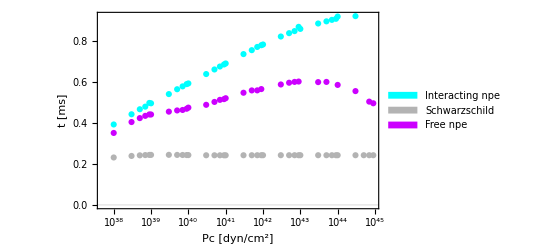

```mathematica
TimesvsPc=ListLogLinearPlot[{Analyst,Analysts,Analystnpe},Joined->False,
PlotStyle->{Hue[0.5],GrayLevel[0.7],Hue[0.8]},
Joined->True,
Frame->True,
FrameLabel->{"Pc [dyn/cm^2]", "t [ms]"},
PlotLegends->Placed[SwatchLegend[{Hue[0.5],GrayLevel[0.7],Hue[0.8]},
{"Interacting npe","Schwarzschild" ,"Free npe"},
LegendMarkers->"Rectangle",
LegendMarkerSize->5,
LegendFunction->(Framed[#,RoundingRadius->0]&),LegendMargins->5],
{Left, Top}],
PlotTheme->"Scientific"]
```

```mathematica
Export["/home/nicolas/Documents/Physics/Bachelors-Dissertation/3-Neutron Stars Densities/Plots/Times_vs_pc.pdf",TimesvsPc];
```

```mathematica
ListPc =Table[10.^ñ,{ñ,45,55}];
AnalysT = {};
Do[{
Pc = ListPc[[ñ]];

Do[{
dener=dener int;
(* TOV eqs*)
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
(**** Interpolation of solutions****)
mass[x_]=M[x]/.solutionTOV[[1]];
pressure[x_]:=p[x]/.solutionTOV[[1]];

(**** Integrate until surface ****)
If[pressure[rad]==0,
Break[],
capR=rad;
];
},{rad,1,30,.01}];
radius = capR/1.5;rstep=0.001;
While[dener[pressure[radius] Pc]/c^2≥ densup ,
(*Print["radius = " , radius, "\t density = ",dener[pressure[radius] Pc]/c^2] ;*)
radius=radius+rstep];

R=radius-rstep;
MStar=mass[R];
ϵ n[x_]:=dener int[pressure[x] Pc]/Pc;

(**** Metric coefficients ****)

grr[r_]:= (1 - 2 α mass[r]/r)^-1;

Bmax =1- (2 α)/R;
BFunction=NDSolve[ {Bb'[r] == -2 Bb[r] pressure'[r]/(pressure[r]+ϵ n[r]),Bb[R]== Bmax},Bb[r],{r,rmin,R}];
gtt[r_]=Bb[r]/.BFunction[[1]];

(****Computing times ****)

ts=t[Rhat[R km, MStar*Subscript[M, sun]]];
tsNS =2 NIntegrate[Sqrt[grr[r] gtt[R]/(gtt[r](gtt[R]-gtt[r]))],{r,rmin,R},MaxRecursion->20]/(10^(-5) c);

Print[Pc,"\t", tsNS],
AnalysT = Append[AnalysT,{Pc,tsNS 10^3 }]
},{ñ,1,Length[ListPc]}]
```

NDSolve::ndsz: At r == 0.001, step size is effectively zero; singularity or stiff system suspected.

1.×10^45	0.000859667

1.×10^46	0.000948576

1.×10^47	0.00100984

1.×10^48	0.0011185

1.×10^49	0.00118955

InterpolatingFunction::dmval: Input value {1.×10^50} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.×10^50	0.00114955

1.×10^51	0.00117877

1.×10^52	0.00127358

1.×10^53	0.00127796

NDSolve::ndsz: At r == 0.001, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.